```mathematica
PacletDirectoryLoad["/Users/nitrika/Projects/Mywork/wolframlanguage/WolframInstitute/NetworkSystem/"]
<<WolframInstitute`NetworkSystem`
```

{/Users/nitrika/Projects/Mywork/wolframlanguage/WolframInstitute/NetworkSystem/}

```mathematica
ClearAll[NetworkSystemRule,CyclicNet,NetworkSystemEvolutionList,NetworkSystemEvolutionPlot,NetworkSystemDisplay]
```

```mathematica
NetworkSystemRule[291,1]
```

{1,{{1}→{{2},{{1},{1}}},{2}→{{1},{{1},{2}}}}}

```mathematica
CyclicNet[5]
```

{{5,2},{1,3},{2,4},{3,5},{4,1}}

```mathematica
NetworkSystemEvolutionList[NetworkSystemRule[291,1],CyclicNet[5],2]
```

{{{},{{5,2},{1,3},{2,4},{3,5},{4,1}}},{{1,1,2,2,3,3,4,4,5,5},{{9,2},{9,3},{1,4},{1,5},{3,6},{3,7},{5,8},{5,9},{7,10},{7,1}}},{{1,1,2,2,3,3,4,4,5,5,6,6,7,7,8,8,9,9,10,10},{{17,2},{17,3},{17,4},{17,5},{1,6},{1,7},{1,8},{1,9},{5,10},{5,11},{5,12},{5,13},{9,14},{9,15},{9,16},{9,17},{13,18},{13,19},{13,20},{13,1}}}}

## Evolution Plots

```mathematica
SimpleRuleMaker[rulenum_]:=Module[{assignment},
assignment=IntegerDigits[rulenum,7,2]/.Thread[Range[7]-1->{{},{1},{2},{1,1},{1,2},{2,1},{2,2}}];

Flatten@Table[{{i}->assignment},{i,1,2}]
]
```

```mathematica
rrr=SimpleRuleMaker[4]
```

{{1}→{{},{1,2}},{2}→{{},{1,2}}}

```mathematica
NetworkSystemEvolutionPlot[{1,rrr},CyclicNet[5],2,"SimpleNet"->False]
```

-Graphics-

```mathematica
gridNet[i_,tot_]:={
Switch[Mod[i,4],
1,Mod[i-4+2,tot],
2,Mod[i-8+2,tot]/. 0->tot,
3,Mod[i+4-2,tot],
0,Mod[i+8-2,tot]
],i+If[Mod[i,4]==0,-2,1]
}
```

```mathematica
treeNet[tot_?OddQ]:=MapIndexed[#&,
Join[Partition[Range[2,tot],2],Table[{n,n},{n,(tot+1)/2,tot}]]]
```

```mathematica
Module[{grid,tree,cyclic,tot=16},
cyclic=CyclicNet[tot];
tree=treeNet[tot+1];
grid=Table[gridNet[i,tot],{i,tot}];
GraphicsColumn[NetworkSystemDisplay/@{cyclic,grid,tree}]
]
```

-Graphics-

```mathematica
With[{tot=5,rules={1,{{1}->#,{2}->#}}&/@{{{2,1},{2}},{{1,1},{2}},{{},{2}},{{},{1}}}},
Map[Framed@NetworkSystemEvolutionPlot[#,CyclicNet[tot],tot+1,"SimpleNet"->True]&,rules]
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{tot=4,rules={1,{{1}->#,{2}->#}}&/@{{{{1},{2}},{2}},{{{2},{1}},{2}}}},
Map[Framed@NetworkSystemEvolutionPlot[#,CyclicNet[1],tot+1]&,rules]
]
```

{-Graphics-,-Graphics-}

```mathematica
Module[{codes={73,78,1118},tot=10},
Map[Framed@NetworkSystemEvolutionPlot[#,CyclicNet[1],tot]&,codes]
]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{tot=15,rule={2,{{1,1}->{{1},{{2,1},{2,1}}},{1,2}->{{{},{1,1}},{{1,1},{}}},{2,1}->{{{},{}},{{1},{2,1}}},{2,2}->{{{1,1},{2,1}},{{2},{2,1}}},{2,3}->{{{},{}},{2}},{2,4}->{{{2,2},{}},{}}}}
},
Framed[NetworkSystemEvolutionPlot[rule,CyclicNet[1],tot]]
]
```

-Graphics-

```mathematica
With[{tot=15,
rule={2,{{1,1}->{{{},{1,1}},{2}},{1,2}->{{2},{{},{}}},{2,1}->{{2,1},{{},{1}}},{2,2}->{{{2},{1}},{}},{2,3}->{{1,2},{2}},{2,4}->{{{1},{1}},{2,1}}}}
},
Framed[NetworkSystemEvolutionPlot[rule,CyclicNet[1],tot]]
]
```

-Graphics-

```mathematica
Module[{tot=9,
rule={2,{{1,1}->{{{1,1},{1}},{2}},{1,2}->{{{1,2},{2}},{{2,2},{}}},{2,1}->{{{2,2},{2}},{{1},{}}},{2,2}->{{{1},{1}},{{2,1},{1,1}}},{2,3}->{{2,1},{2}},{2,4}->{{{1},{1,2}},{{1,2},{}}}}}
},
Framed[NetworkSystemEvolutionPlot[rule,CyclicNet[1],tot]]
]
```

-Graphics-

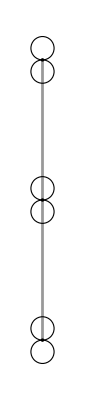
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NetworkSystemEvolutionPlot[#,CyclicNet[1],2]&/@Range[70,90]
```

## Depth One

```mathematica
36^2
```

1296

```mathematica
IntegerDigits[219,36,2]
```

{6,3}

```mathematica
IntegerDigits[219,6,4]
```

{1,0,0,3}

```mathematica
IntegerDigits[#,6,2]&/@IntegerDigits[219,36,2]/.{0->{1},1->{2},2->{{1},{1}},3->{{1},{2}},4->{{2},{1}},5->{{2},{2}}}
```

{{{2},{1}},{{1},{{1},{2}}}}

```mathematica
GetRulesN[219]
```

{1,{{1}→{{2},{1}},{2}→{{1},{{1},{2}}}}}

```mathematica
GetRules[219]
```

{1,{{1,j}→{{2},{1}},{2,j}→{{1},{{1},{2}}}}}

```mathematica
GetRulesN[code_Integer]:={1,Table[{i}->(IntegerDigits[#,6,2]&/@IntegerDigits[219,36,2]/.{0->{1},1->{2},2->{{1},{1}},3->{{1},{2}},4->{{2},{1}},5->{{2},{2}}})[[i]],{i,2}]}
```

```mathematica
Flatten[Array[{{##}->1}&,Table[2^i,{i,2}]]]
```

{{1,1}→1,{1,2}→1,{1,3}→1,{1,4}→1,{2,1}→1,{2,2}→1,{2,3}→1,{2,4}→1}

```mathematica
GetRules[code_Integer]:={1,Table[{i}->Table[{{1},{2},{{1},{1}},{{1},{2}},{{2},{1}},{{2},{2}}}[[1+IntegerDigits[code,6,4][[1+2 (i-1)+(j-1)]]]],{j,2}],{i,2}]}
```

```mathematica
Array[{{##}->#2}&,Table[2^i,{i,2}]]
```

{{{{1,1}→1},{{1,2}→2},{{1,3}→3},{{1,4}→4}},{{{2,1}→1},{{2,2}→2},{{2,3}→3},{{2,4}→4}}}

```mathematica
Array[{{##}->#}&,Table[2^i,{i,1}]]
```

{{{1}→1},{{2}→2}}

```mathematica
42^2
```

1764

```mathematica
1+IntegerDigits[5060443886396,1764,4]
```

{922,1622,902,1593}

```mathematica
IntegerDigits[219,36,2]
```

{6,3}

```mathematica
Flatten[Array[{##}&,Table[2^i,{i,3}]],1]
```

{{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,1,7},{1,1,8}},{{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,2,7},{1,2,8}},{{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,3,6},{1,3,7},{1,3,8}},{{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,4,6},{1,4,7},{1,4,8}},{{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5},{2,1,6},{2,1,7},{2,1,8}},{{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5},{2,2,6},{2,2,7},{2,2,8}},{{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,3,6},{2,3,7},{2,3,8}},{{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5},{2,4,6},{2,4,7},{2,4,8}}}

```mathematica
Table[Table[1+2(i-1)+(j-1),{j,2}],{i,2^3}]
```

{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16}}

```mathematica
Table[2^i,{i,4}]
```

{2,4,8,16}

```mathematica
NestList[{#[[1]]+1,2^#[[1]]}&,{1,1},4][[All,2]]
```

{1,2,4,8,16}

```mathematica
RandomInteger[{0,3}]
```

0

```mathematica
Table[RandomInteger[],{RandomInteger[{0,2}]}]
```

{1}

```mathematica
Table[{{1},{2},{{1},{1}},{{1},{2}},{{2},{1}},{{2},{2}}}[[1+IntegerDigits[code,6,4][[1+2 (i-1)+(j-1)]]]],{j,2}]
```

```mathematica
fbsix[code_,pad_]:=Replace[IntegerDigits[code,6,pad],{{1,0,x_}:>x,{1|0,x_,y_}:>{x,y}}]
```

```mathematica
Flatten[Array[{##}&,Table[2^i,{i,2}]],1][[6]]
```

{2,2}

```mathematica
{1->{1},2->{2},3->{1,1},4->{1,2},5->{2,1},6->{2,2}}
```

{1→{1},2→{2},3→{1,1},4→{1,2},5→{2,1},6→{2,2}}

```mathematica
{{2|3}->{{{1,2},{1,2}},{1,2}},{4}->{{1,1},{{2,1},{2}}},{5}->{{{1,2},{1,2}},{{1,2},{2}}},{6}->{{2},{1,1}}}//Column
```

{2|3}→{{{1,2},{1,2}},{1,2}}
{4}→{{1,1},{{2,1},{2}}}
{5}→{{{1,2},{1,2}},{{1,2},{2}}}
{6}→{{2},{1,1}}

```mathematica
{{2|3}->{{{1,2},{1,2}},{1,2}},{4}->{{1,1},{{2,1},{2}}},{5}->{{{1,2},{1,2}},{{1,2},{2}}},{6}->{{2},{1,1}}}//Column
```

{2|3}→{{{1,2},{1,2}},{1,2}}
{4}→{{1,1},{{2,1},{2}}}
{5}→{{{1,2},{1,2}},{{1,2},{2}}}
{6}→{{2},{1,1}}

```mathematica
With[{d=2,code=5060443886396},
MapThread[#2->#&,{1+fbsix[#,3]&/@IntegerDigits[code,Times@@NestList[(#+1)&,6,d-1],2^(d+1)],Flatten[Array[{##}&,Table[2^i,{i,2}]],1]}]
]
```

{{1,1}→{4,4},{1,2}→4,{1,3}→3,{1,4}→{5,2},{2,1}→{4,4},{2,2}→{4,2},{2,3}→2,{2,4}→3}

```mathematica
IntegerDigits[3,6,4]
```

{0,0,0,3}

```mathematica
Times@@NestList[(#+1)&,6,2-1]
```

42

```mathematica
42^8
```

9682651996416

```mathematica
IntegerDigits[968265199641,Times@@NestList[(#+1)&,6,2-1],2^3]
```

{4,8,16,33,25,8,16,33}

```mathematica
NestList[Sqrt[#]&,9682651996416,4]
```

{9682651996416,3111696,1764,42,√42}

```mathematica
With[{d=2},
NestList[#^2&,Times@@NestList[(#+1)&,6,d-1],d+1]
]
```

{42,1764,3111696,9682651996416}

```mathematica
6 7 8
```

336

```mathematica
Sqrt[26389334508755778116918569912191456116736]
```

162447943996702457856

```mathematica
Times[Range[1,10]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Times@@NestList[(#+1)&,6,2-1]
```

42

```mathematica
NestList[#^2&,6,4]
```

{6,36,1296,1679616,2821109907456}

```mathematica
IntegerDigits[336,]
```

```mathematica
IntegerDigits[219,6,2^2]
```

{1,0,0,3}

```mathematica
NestList[Sqrt[#]&,1296,10]
```

{1296,36,6,√6,6^(1/4),6^(1/8),6^(1/16),6^(1/32),6^(1/64),6^(1/128),6^(1/256)}

```mathematica
IntegerDigits[#,42,2]&/@IntegerDigits[5060443886396,1764,4]
```

{{21,39},{38,25},{21,19},{37,38}}

```mathematica
RandomDNRuleR[depth_Integer,code_]:={depth,Flatten[Array[({##}->Table[Table[{{1},{2},{{1},{1}},{{1},{2}},{{2},{1}},{{2},{2}}}[[1+IntegerDigits[code,6,4][[1+2 (i-1)+(j-1)]]]],{j,2}],{i,2}])&,Table[2^i,{i,depth}]]]
}
```

```mathematica
RandomDNRuleR[2,219][[2]]//Column
```

{1,1}→{{{2},{1}},{{1},{{1},{2}}}}
{1,2}→{{{2},{1}},{{1},{{1},{2}}}}
{1,3}→{{{2},{1}},{{1},{{1},{2}}}}
{1,4}→{{{2},{1}},{{1},{{1},{2}}}}
{2,1}→{{{2},{1}},{{1},{{1},{2}}}}
{2,2}→{{{2},{1}},{{1},{{1},{2}}}}
{2,3}→{{{2},{1}},{{1},{{1},{2}}}}
{2,4}→{{{2},{1}},{{1},{{1},{2}}}}

```mathematica
294/6
```

49

```mathematica
6*6
```

36

```mathematica
6*6*7*7
```

```mathematica
1764
```

1764

```mathematica
112896^6
```

2070481377455157458127600746496

```mathematica
Subsets[{{1},{2},{1,1},{1,2},{2,1},{2,2}},2]
```

{{},{{1}},{{2}},{{1,1}},{{1,2}},{{2,1}},{{2,2}},{{1},{2}},{{1},{1,1}},{{1},{1,2}},{{1},{2,1}},{{1},{2,2}},{{2},{1,1}},{{2},{1,2}},{{2},{2,1}},{{2},{2,2}},{{1,1},{1,2}},{{1,1},{2,1}},{{1,1},{2,2}},{{1,2},{2,1}},{{1,2},{2,2}},{{2,1},{2,2}}}

```mathematica
RandomDNRule[depth_Integer,newprob_]:={depth,Flatten[Array[({##}->1+Table[If[Random[]<newprob,Table[Table[Random[Integer],{Random[Integer,{0,2}]}],{2}],Table[Random[Integer],{Random[Integer,{0,3}]}]],{2}])&,
Table[2^i,{i,depth}]
]
]}
```

```mathematica
Union[Flatten[Array[{{##}->Plus@##}&,Table[2^i,{i,3}]],2]]
```

{{{1,1,1}→3},{{1,1,2}→4},{{1,1,3}→5},{{1,1,4}→6},{{1,1,5}→7},{{1,1,6}→8},{{1,1,7}→9},{{1,1,8}→10},{{1,2,1}→4},{{1,2,2}→5},{{1,2,3}→6},{{1,2,4}→7},{{1,2,5}→8},{{1,2,6}→9},{{1,2,7}→10},{{1,2,8}→11},{{1,3,1}→5},{{1,3,2}→6},{{1,3,3}→7},{{1,3,4}→8},{{1,3,5}→9},{{1,3,6}→10},{{1,3,7}→11},{{1,3,8}→12},{{1,4,1}→6},{{1,4,2}→7},{{1,4,3}→8},{{1,4,4}→9},{{1,4,5}→10},{{1,4,6}→11},{{1,4,7}→12},{{1,4,8}→13},{{2,1,1}→4},{{2,1,2}→5},{{2,1,3}→6},{{2,1,4}→7},{{2,1,5}→8},{{2,1,6}→9},{{2,1,7}→10},{{2,1,8}→11},{{2,2,1}→5},{{2,2,2}→6},{{2,2,3}→7},{{2,2,4}→8},{{2,2,5}→9},{{2,2,6}→10},{{2,2,7}→11},{{2,2,8}→12},{{2,3,1}→6},{{2,3,2}→7},{{2,3,3}→8},{{2,3,4}→9},{{2,3,5}→10},{{2,3,6}→11},{{2,3,7}→12},{{2,3,8}→13},{{2,4,1}→7},{{2,4,2}→8},{{2,4,3}→9},{{2,4,4}→10},{{2,4,5}→11},{{2,4,6}→12},{{2,4,7}→13},{{2,4,8}→14}}

```mathematica
Union[{2,3,4,5,3,4,5,6}]
```

{2,3,4,5,6}

```mathematica
{{1,1},{1,2},{1,3},{1,4},{2,1},{2,2},{2,3},{2,4}}
```

```mathematica
NeighborNumbersT[list_,i_Integer,d_Integer]:=Map[Length,NestList[Union[Flatten[list⟦#⟧]]&,Union[list⟦i⟧],d-1]]
```

```mathematica
NeighborNumbersT[CyclicNet[5],1,3]
```

{2,3,4}

```mathematica
2^2
```

4

```mathematica
base1764=IntegerDigits[5060423232343886396,1764,3];
```

```mathematica
base42=Flatten[IntegerDigits[#,42,2]&/@base1764,1]
```

{12,19,41,21,17,38}

```mathematica
Flatten[Array[{##}&,Table[2^i,{i,2}]],1]
```

```mathematica
Plus@@@{{1,1},{1,2},{2,1},{2,2},{2,3},{2,4}}
```

{2,3,3,4,5,6}

```mathematica
Plus@@{1,2,2,4,6,8}
```

23

```mathematica
2*1
```

2

```mathematica
NeighborNumbers[depth_]:=Module[{gen},
gen[{seq___,last_}]:=Select[Table[Append[{seq,last},next],{next,last,2 last}],#[[-1]]<=2 #[[-2]]&];
Flatten[NestList[Flatten[#,1]&,{{1},{2}},depth-1],1]]

NeighborNumbers[2]
```

{{1},{2},1,2}

```mathematica
GenerateNeighborNumbers[d_]:=Module[{pairs},pairs=Flatten[Table[{a,b},{a,1,d},{b,1,Min[2 a,d]}],1];
Sort[pairs]]
validNeighbors=GenerateNeighborNumbers[3];
```

```mathematica
validNeighbors
```

{{1,1},{1,2},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

```mathematica
IntegerDigits[219,6,4]
```

{1,0,0,3}

## Depth Two

```mathematica
1764^4
```

9682651996416

```mathematica
ccc=CyclicNet[5]
```

{{5,2},{1,3},{2,4},{3,5},{4,1}}

```mathematica
Length/@NestList[Union[Flatten[ccc[[#]]]]&,Union[ccc[[5]]],2-1]
```

{2,3}

```mathematica
IntegerDigits[5060443886396,1764,4]
```

{921,1621,901,1592}

```mathematica
(IntegerDigits[#,42,2]&/@IntegerDigits[5060443886396,1764,4])
```

{{21,39},{38,25},{21,19},{37,38}}

```mathematica
fbsix[code_,pad_]:=Replace[IntegerDigits[code,6,pad],{{1,0,x_}:>x,{1|0,x_,y_}:>{x,y}}]
```

```mathematica
list=1+{fbsix[#[[1]],3],fbsix[#[[2]],3]}&/@(IntegerDigits[#,42,2]&/@IntegerDigits[5060443886396,1764,4]);
```

```mathematica
list
```

{{{4,4},4},{3,{5,2}},{{4,4},{4,2}},{2,3}}

```mathematica
Flatten[list,1]
```

{{3,3},3,2,{4,1},{3,3},{3,1},1,2}

```mathematica
(IntegerDigits[#,42,2]&/@IntegerDigits[5060443886396,1764,4])
```

{{21,39},{38,25},{21,19},{37,38}}

```mathematica
rcases=MapIndexed[{#2[[1]]+2/.{3->2|3}}->#&,list/.{1->{1},2->{2},3->{1,1},4->{1,2},5->{2,1},6->{2,2}}]
```

```mathematica
{2}/.{{2|3}->{{{1,2},{1,2}},{1,2}},{4}->{{1,1},{{2,1},{2}}},{5}->{{{1,2},{1,2}},{{1,2},{2}}},{6}->{{2},{1,1}}}
```

{{{1,2},{1,2}},{1,2}}

```mathematica
DNRule[depth_Integer,index_Integer]:={depth,Flatten[Array[({##}->{Plus@##}/.rcases)&,Table[2^i,{i,depth}]]]}
```

```mathematica
DNRule[2,449949494994]
```

{2,{{1,1}→{{{1,2},{1,2}},{1,2}},{1,2}→{{{1,2},{1,2}},{1,2}},{1,3}→{{1,1},{{2,1},{2}}},{1,4}→{{{1,2},{1,2}},{{1,2},{2}}},{2,1}→{{{1,2},{1,2}},{1,2}},{2,2}→{{1,1},{{2,1},{2}}},{2,3}→{{{1,2},{1,2}},{{1,2},{2}}},{2,4}→{{2},{1,1}}}}

```mathematica
GetDepthXRules[index_,depth_]:=Module[{list,f,rcases},
f[code_]:=Replace[IntegerDigits[code,6,3],{{1,0,x_}:>x,{1|0,x_,y_}:>{x,y}}];
list=1+{f[#[[1]]],f[#[[2]]]}&/@(IntegerDigits[#,216,2]&/@IntegerDigits[index,46656,4]);
rcases=MapIndexed[{#2[[1]]+2/.{3->2|3}}->#&,list/.{1->{1},2->{2},3->{1,1},4->{1,2},5->{2,1},6->{2,2}}];
{depth,Flatten[Array[({##}->{Plus@##}/.rcases)&,Table[2^i,{i,depth}]]]}
]
```

```mathematica
2^(3+1)-3-1
```

12

```mathematica
Range[2,2^(2+1)-2]
```

{2,3,4,5,6}

```mathematica
6^2
```

```mathematica
36^2
```

1296

```mathematica
2
```

```mathematica
6^(5+1)
```

46656

```mathematica
IntegerDigits[219,6,2]
```

{0,3}

```mathematica
GetDepthXRules[5060443886396,2]
```

{2,{{1,1}→{{{1},{1}},{{1},{1}}},{1,2}→{{{1},{1}},{{1},{1}}},{1,3}→{{{2},{2,1}},{{2,1},{1,2},{1,1}}},{1,4}→{{{2,1},{1,1},{1,1}},{{2,2},{1,2},{2,1}}},{2,1}→{{{1},{1}},{{1},{1}}},{2,2}→{{{2},{2,1}},{{2,1},{1,2},{1,1}}},{2,3}→{{{2,1},{1,1},{1,1}},{{2,2},{1,2},{2,1}}},{2,4}→{{{2,1},{2,1},{1,2}},{{1,2},{2},{1,1}}}}}

```mathematica
{2,{{1,1}->{{{1,2},{1,2}},{1,2}},{1,2}->{{{1,2},{1,2}},{1,2}},{1,3}->{{1,1},{{2,1},{2}}},{1,4}->{{{1,2},{1,2}},{{1,2},{2}}},{2,1}->{{{1,2},{1,2}},{1,2}},{2,2}->{{1,1},{{2,1},{2}}},{2,3}->{{{1,2},{1,2}},{{1,2},{2}}},{2,4}->{{2},{1,1}}}}
```

{2,{{1,1}→{{{1,2},{1,2}},{1,2}},{1,2}→{{{1,2},{1,2}},{1,2}},{1,3}→{{1,1},{{2,1},{2}}},{1,4}→{{{1,2},{1,2}},{{1,2},{2}}},{2,1}→{{{1,2},{1,2}},{1,2}},{2,2}→{{1,1},{{2,1},{2}}},{2,3}→{{{1,2},{1,2}},{{1,2},{2}}},{2,4}→{{2},{1,1}}}}

```mathematica
list/.{1->{1},2->{2},3->{1,1},4->{1,2},5->{2,1},6->{2,2}}
```

{{{{1,2},{1,2}},{1,2}},{{1,1},{{2,1},{2}}},{{{1,2},{1,2}},{{1,2},{2}}},{{2},{1,1}}}

```mathematica
Table[i/.{3->2|3},{i,3,6}]
```

{2|3,4,5,6}

```mathematica
Table[i+2,{i,4}]
```

{3,4,5,6}

```mathematica
6^3
```

216

```mathematica
IntegerDigits[#,6,2]&/@IntegerDigits[219,36,2]
```

```mathematica
{{1,0},{0,3}}/.{0->{1},1->{2},2->{{1},{1}},3->{{1},{2}},4->{{2},{1}},5->{{2},{2}}}
```

{{{2},{1}},{{1},{{1},{2}}}}

```mathematica
Table[Table[Table[Random[Integer],{Random[Integer,{0,2}]}],{2}],{2}]
```

{{{1,1},{}},{{1,1},{1,0}}}

```mathematica
Replace[{1,0,2},{{1,0,x_}:>x,{1|0,x_,y_}:>{x,y}}]
```

2

```mathematica
Table[2^i,{i,2}]
```

{2,4}

```mathematica
IntegerDigits[5060443886396,1764,4]
```

{921,1621,901,1592}

```mathematica
{2|3->{21,39}}
```

```mathematica
2/.{2|3->{21,39}}
```

{21,39}

```mathematica
IntegerDigits[21,6,3]
```

{0,3,3}

```mathematica
Table[2^i,{i,2}]
```

{2,4}

```mathematica
DNRule[depth_Integer,index_Integer]:={depth,Flatten[Array[({##}->r)&,Table[2^i,{i,depth}]]]}
```

```mathematica
DNRule[2,3]
```

{2,{{1,1}→r,{1,2}→r,{1,3}→r,{1,4}→r,{2,1}→r,{2,2}→r,{2,3}→r,{2,4}→r}}

```mathematica
RandomInteger[{0,3}]
```

1

```mathematica
Table[Table[Table[Random[Integer],{Random[Integer,{0,2}]}],{2}],{2}]
```

{{{1,0},{}},{{0,0},{0,1}}}

```mathematica
Table[Random[Integer],{Random[Integer,{0,2}]}]
```

{1,0}

```mathematica
Mod[Random[],10]
```

0.0137434

```mathematica
RandomDNRule[1,0]
```

{1,{{1}→{{},{1,1,1}},{2}→{{},{2,1}}}}

```mathematica
Random[Integer,{0,2}]
```

2

```mathematica
1+Table[Table[Table[Random[Integer],{2}],{2}],{2}]
```

{{{2,2},{2,2}},{{2,1},{1,1}}}

```mathematica
Table[2^i,{i,1}]
```

{2}

```mathematica
Table[{{1},{2},{1,1},{1,2},{2,1},{2,2}},{j,2}]
```

{{{1},{2},{1,1},{1,2},{2,1},{2,2}},{{1},{2},{1,1},{1,2},{2,1},{2,2}}}

```mathematica
Array[{##}&,Table[2^i,{i,2}]]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}}}

```mathematica
Flatten[Array[({##}->1)&,Table[2^i,{i,2}]]]
```

{{1,1}→1,{1,2}→1,{1,3}→1,{1,4}→1,{2,1}→1,{2,2}→1,{2,3}→1,{2,4}→1}

```mathematica
RuleMakerNodes[rulenum_]:=Table[Rule[{i},(IntegerDigits[rulenum,21,2]/.Thread[Range[21]-1->Join[{{1},{2},{1,1},{1,2},{2,1},{2,2}},Drop[Subsets[{{1},{2},{1,1},{1,2},{2,1},{2,2}},2],7]]])],{i,1,2}]
```

```mathematica
IntegerDigits[244,21,2]
```

{11,13}

```mathematica
RuleMakerNodes[299]
```

{{1}→{{{2},{2,2}},{2,2}},{2}→{{{2},{2,2}},{2,2}}}

```mathematica
Thread[Range[21]-1->Join[{{1},{2},{1,1},{1,2},{2,1},{2,2}},Drop[Subsets[{{1},{2},{1,1},{1,2},{2,1},{2,2}},2],7]]]
```

{0→{1},1→{2},2→{1,1},3→{1,2},4→{2,1},5→{2,2},6→{{1},{2}},7→{{1},{1,1}},8→{{1},{1,2}},9→{{1},{2,1}},10→{{1},{2,2}},11→{{2},{1,1}},12→{{2},{1,2}},13→{{2},{2,1}},14→{{2},{2,2}},15→{{1,1},{1,2}},16→{{1,1},{2,1}},17→{{1,1},{2,2}},18→{{1,2},{2,1}},19→{{1,2},{2,2}},20→{{2,1},{2,2}}}

```mathematica
Drop[Subsets[{{1},{2},{1,1},{1,2},{2,1},{2,2}},2],7]
```

{{{1},{2}},{{1},{1,1}},{{1},{1,2}},{{1},{2,1}},{{1},{2,2}},{{2},{1,1}},{{2},{1,2}},{{2},{2,1}},{{2},{2,2}},{{1,1},{1,2}},{{1,1},{2,1}},{{1,1},{2,2}},{{1,2},{2,1}},{{1,2},{2,2}},{{2,1},{2,2}}}

```mathematica
{1,Table[{i}->,{i,2}]}
```

{1,{{{1}}→{{1},{{2},{2}},{{1},{2}},{{2},{2}}},{{2}}→{{1},{{2},{2}},{{1},{2}},{{2},{2}}}}}

```mathematica
Table[{{1},{2},{{1},{1}},{{1},{2}},{{2},{1}},{{2},{2}}}[[1+IntegerDigits[203,6,4][[1+2 (2-1)+(j-1)]]]],{j,2}]
```

{{{1},{2}},{{2},{2}}}

```mathematica
1+IntegerDigits[203,6,4]/.{1->{1},2->{2},3->{{1},{1}},4->{{1},{2}},5->{{2},{1}},6->{{2},{2}}}
```

{{1},{{2},{2}},{{1},{2}},{{2},{2}}}

```mathematica
1+IntegerDigits[203,6,4]
```

{1,6,4,6}

```mathematica
GetRules[code_Integer]:={1,Table[{i}->Table[{{1},{2},{{1},{1}},{{1},{2}},{{2},{1}},{{2},{2}}}[[1+IntegerDigits[code,6,4][[1+2 (i-1)+(j-1)]]]],{j,2}],{i,2}]}
```

```mathematica
GetRules[219]
```

{1,{{1}→{{2},{1}},{2}→{{1},{{1},{2}}}}}

```mathematica
Table[i,{i,2}]
```

{1,2}

```mathematica
IntegerDigits[203,6,4]
```

{0,5,3,5}

```mathematica
Table[{i}->Table[{{1},{2},{{1},{1}},{{1},{2}},{{2},{1}},{{2},{2}}}[[1+IntegerDigits[203,6,4][[1+2(i-1)+(j-1)]]]],{j,2}],{i,2}]
```

{{1}→{{1},{{2},{2}}},{2}→{{{1},{2}},{{2},{2}}}}

```mathematica
Array[{##}&,Table[2^i,{i,2}]]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}}}

```mathematica
Table[Table[1+{j-1+i-1},{j,2}],{i,4}]
```

{{{1},{2}},{{2},{3}},{{3},{4}},{{4},{5}}}

```mathematica
sss={{1},{2},{1,1},{1,2},{2,1},{2,2}};
```

```mathematica
Table[{i}->{{1},{2},{1,1},{1,2},{2,1},{2,2}}[[1+IntegerDigits[203,6,4][[1+2(i-1)+(j-1)]]]],{j,2},{i,2}]
```

{{{1}→{1},{2}→{1,2}},{{1}→{2,2},{2}→{2,2}}}

```mathematica
DNAllRule[code_Integer]:=Module[{dd},
dd=IntegerDigits[code,6,4];
{1,Table[{i}->Table[{{1},{2},{{1},{1}},{{1},{2}},{{2},{1}},{{2},{2}}}[[1+dd[[1+2(i-1)+(j-1)]]]],{j,2}],{i,2}]}]
```

```mathematica
6^4
```

1296

## Depth X

Sum of distinct neighbours:

```mathematica
d=1;(*Depth/distance to the neighbours*)
```

```mathematica
2^(d+1)-2
```

2

```mathematica
possibleSums[d_]:=Range[d,2^(d+1)-2];
```

```mathematica
possibleSums[d]
```

{1,2}

Link instructions for d: (use base-6)

```mathematica
6^(d)
```

36

```mathematica
Clear[linkSpaceSize]
```

```mathematica
linkSpaceSize[d_]:=6^(d)
```

```mathematica
caseSpaceSize[d_]:=(linkSpaceSize[d])^2
```

```mathematica
caseSpaceSize[d]
```

36

```mathematica
Range[0,5]
```

{0,1,2,3,4,5}

```mathematica
decodeOneLink[code_,d_]:=Module[{f,baseDigits,res,basemap},
f[i_]:=IntegerDigits[i,6,d+1];
baseDigits=If[!MemberQ[Range[0,5],code],f[code],code];
basemap=If[d==1,
{0->{1},1->{2},2->{{1},{1}},3->{{1},{2}},4->{{2},{1}},5->{{2},{2}}},{0->{1},1->{2},2->{1,1},3->{1,2},4->{2,1},5->{2,2}}
];
res=baseDigits/.basemap;
res
]
```

```mathematica
d=1
```

1

```mathematica
decodeOneLink[3,d]
```

{{1},{{1},{2}}}

```mathematica
decodeOneCaseIndex[indexCase_,d_]:=Module[{sz=linkSpaceSize[d],upNum,downNum},
upNum =Quotient[indexCase,sz];
downNum=Mod[indexCase,sz];
{decodeOneLink[upNum,d],decodeOneLink[downNum,d]}
]
```

```mathematica
IntegerDigits[219,36,2]
```

{6,3}

```mathematica
decodeDistanceDRule[index_,d_]:=Module[
{
sums=possibleSums[d],
c=Length[possibleSums[d]],
caseIndices,base,iCase,caseInstr
},
base=caseSpaceSize[d];
If[index>=base^c,Return["Index out of range for distance="<>ToString[d]<>". Max index is "<>ToString[base^c-1]];
];
caseIndices=IntegerDigits[index,base,c];
AssociationThread[sums,decodeOneCaseIndex[#,d]&/@caseIndices]
]
```

```mathematica
decodeDistanceDRule[219,1]
```

<|1→{{2},{1}},2→{{1},{{1},{2}}}|>

```mathematica
GetDepthDRules[index_,d_]:=Module[{cases,sums,localDomain,finalMapping},
cases=decodeDistanceDRule[index,d];
If[!AssociationQ[cases],Return[cases]];
sums=Keys[cases];
Flatten[Array[{{##}->cases[Total[{##}]]}&,Table[2^i,{i,d}]]]
]
```

```mathematica
testcase1=219;
testcase2=5060443886396;
d=2;
```

```mathematica
GetDepthDRules[testcase2,d]
```

{{1,1}→{{1},{2}},{1,2}→{{{1},{2,1},{2,1}},{{1},{1,2},{1,1}}},{1,3}→{{{1},{2,1},{1,1}},{{1},{1,1},{2,2}}},{1,4}→{{{1},{1,2},{2,1}},{{1},{2,1},{2,1}}},{2,1}→{{{1},{2,1},{2,1}},{{1},{1,2},{1,1}}},{2,2}→{{{1},{2,1},{1,1}},{{1},{1,1},{2,2}}},{2,3}→{{{1},{1,2},{2,1}},{{1},{2,1},{2,1}}},{2,4}→{{{1},{1,2},{1,2}},{{1},{2},{1,1}}}}

```mathematica
Array[{##}&,Table[2^i,{i,2}]]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}}}

```mathematica
GetDepthOneRulesT[code_Integer]:={1,Table[{i}->Table[{{1},{2},{{1},{1}},{{1},{2}},{{2},{1}},{{2},{2}}}[[1+IntegerDigits[code,6,4][[1+2 (i-1)+(j-1)]]]],{j,2}],{i,2}]}
```

```mathematica
GetDepthOneRulesT[1118]
```

{1,{{1}→{{{2},{2}},{2}},{2}→{{1},{{1},{1}}}}}

```mathematica
{1,GetDepthDRules[1118,1]}
```

{1,{{1}→{{{2},{2}},{2}},{2}→{{1},{{1},{1}}}}}

```mathematica
IntegerDigits[100,6,3]
```

{2,4,4}

## Putting it all together[Rule Generation]

```mathematica
decodeOneLink[code_,d_]:=Module[{f,baseDigits,basemap},
f[i_]:=IntegerDigits[i,6,d+1];
baseDigits=If[!MemberQ[Range[0,5],code],f[code],{code}];
basemap=If[d==1,
{0->{1},1->{2},2->{{1},{1}},3->{{1},{2}},4->{{2},{1}},5->{{2},{2}}},{0->{1},1->{2},2->{1,1},3->{1,2},4->{2,1},5->{2,2}}
];
(1+Replace[baseDigits,{{1,0,x_}:>x,{1|0,x_,y_}:>{x,y}}])/.basemap
]
```

```mathematica
decodeOneCaseIndex[indexcase_,d_]:=Module[{sz=6^d,up,down},
up=Quotient[indexcase,sz];
down=Mod[indexcase,sz];
{decodeOneLink[up,d],decodeOneLink[down,d]}
]
```

```mathematica
GDepthRules[index_,d_]:=Module[{cases,localpairs,c,base=(6^d)^2},
localpairs=Tuples[Table[Range[1,2^k],{k,d}]];
c=Length[localpairs];
If[index>=base^c,
Return["Index out of range for distance="<>ToString[d]<>". Max index is "<>ToString[base^c-1]];
];
MapThread[If[IntegerQ[#],{#},#]->#2&,
{localpairs,decodeOneCaseIndex[#,d]&/@IntegerDigits[index,base,c]}]
]
```

```mathematica
{2,GetDepthDRules[5060443886396,2]}
```

```mathematica
{1,GDepthRules[45060443886396,2]}
```

```mathematica
GDepthRules[5060443886396,3]
```

{{1,1,1}→{{{1}},{{1}}},{1,1,2}→{{{1}},{{1}}},{1,1,3}→{{{1}},{{1}}},{1,1,4}→{{{1}},{{1}}},{1,1,5}→{{{1}},{{1}}},{1,1,6}→{{{1}},{{1}}},{1,1,7}→{{{1}},{{1}}},{1,1,8}→{{{1}},{{1}}},{1,2,1}→{{{1}},{{1}}},{1,2,2}→{{{1}},{{1}}},{1,2,3}→{{{1}},{{1}}},{1,2,4}→{{{1}},{{1}}},{1,2,5}→{{{1}},{{1}}},{1,2,6}→{{{1}},{{1}}},{1,2,7}→{{{1}},{{1}}},{1,2,8}→{{{1}},{{1}}},{1,3,1}→{{{1}},{{1}}},{1,3,2}→{{{1}},{{1}}},{1,3,3}→{{{1}},{{1}}},{1,3,4}→{{{1}},{{1}}},{1,3,5}→{{{1}},{{1}}},{1,3,6}→{{{1}},{{1}}},{1,3,7}→{{{1}},{{1}}},{1,3,8}→{{{1}},{{1}}},{1,4,1}→{{{1}},{{1}}},{1,4,2}→{{{1}},{{1}}},{1,4,3}→{{{1}},{{1}}},{1,4,4}→{{{1}},{{1}}},{1,4,5}→{{{1}},{{1}}},{1,4,6}→{{{1}},{{1}}},{1,4,7}→{{{1}},{{1}}},{1,4,8}→{{{1}},{{1}}},{2,1,1}→{{{1}},{{1}}},{2,1,2}→{{{1}},{{1}}},{2,1,3}→{{{1}},{{1}}},{2,1,4}→{{{1}},{{1}}},{2,1,5}→{{{1}},{{1}}},{2,1,6}→{{{1}},{{1}}},{2,1,7}→{{{1}},{{1}}},{2,1,8}→{{{1}},{{1}}},{2,2,1}→{{{1}},{{1}}},{2,2,2}→{{{1}},{{1}}},{2,2,3}→{{{1}},{{1}}},{2,2,4}→{{{1}},{{1}}},{2,2,5}→{{{1}},{{1}}},{2,2,6}→{{{1}},{{1}}},{2,2,7}→{{{1}},{{1}}},{2,2,8}→{{{1}},{{1}}},{2,3,1}→{{{1}},{{1}}},{2,3,2}→{{{1}},{{1}}},{2,3,3}→{{{1}},{{1}}},{2,3,4}→{{{1}},{{1}}},{2,3,5}→{{{1}},{{1}}},{2,3,6}→{{{1}},{{1}}},{2,3,7}→{{{1}},{{1}}},{2,3,8}→{{{1}},{{1}}},{2,4,1}→{{{1}},{{1}}},{2,4,2}→{{{1}},{{1}}},{2,4,3}→{{{1}},{{1}}},{2,4,4}→{{{1}},{{1}}},{2,4,5}→{{{1}},{{1}}},{2,4,6}→{{{1},{1},{2},{2,1}},{{1},{2,1},{1,2},{1,1}}},{2,4,7}→{{{1},{2,1},{1,1},{1,1}},{{1},{2,2},{1,2},{2,1}}},{2,4,8}→{{{1},{2,1},{2,1},{1,2}},{{1},{1,2},{2},{1,1}}}}

```mathematica
d=2;
```

```mathematica
NestList[(#+1)&,6,d-1]
```

{6,7}

```mathematica
IntegerDigits[5060443886396,Times@@NestList[(#+1)&,6,d-1],2^(d+1)]
```

{3,3,1,2}

```mathematica
test=GDepthRules[largecode,3];
```

```mathematica
Labeled[Grid[Prepend[KeyValueMap[{#1,#2[[1]],#2[[2]]}&,Association[test]],{"Configuration","Up Link","Down Link"}],Frame->All,Alignment->{Left,Top},Spacings->{5, 1}],"Rule Index: "<>ToString[9652665412472289834238],Top]
```

Configuration | Up Link | Down Link
{1,1,1} | {{1},{1,2},{1,2},{2,1}} | {{1},{2},{1,1},{2,1}}
{1,1,2} | {{1},{2},{1,1},{2}} | {{1},{2,1},{1,1},{1,1}}
{1,1,3} | {{1},{2,1},{1,1},{1}} | {{1},{1,1},{2,2},{1}}
{1,1,4} | {{1},{1,1},{2},{1,2}} | {{1},{2},{2},{2,1}}
{1,1,5} | {{1},{1,1},{1,2},{2}} | {{1},{2,1},{2,2},{1,1}}
{1,1,6} | {{1},{2,2},{2,1},{2,2}} | {{1},{2,2},{1,2},{1,2}}
{1,1,7} | {{1},{2,2},{2,1},{1}} | {{1},{1,2},{2},{2,1}}
{1,1,8} | {{1},{2},{2},{2,1}} | {{1},{1},{2},{1,1}}
{1,2,1} | {{1},{1,2},{1},{1,2}} | {{1},{2,1},{1},{1,1}}
{1,2,2} | {{1},{1},{1,1},{2}} | {{1},{2},{1,1},{2,2}}
{1,2,3} | {{1},{2,2},{2,1},{2,1}} | {{1},{2,1},{2,1},{2,2}}
{1,2,4} | {{1},{2,1},{2,2},{2,2}} | {{2,2}}
{1,2,5} | {{1},{2,2},{2,1},{1}} | {{1},{2,1},{2},{1}}
{1,2,6} | {{1},{1,1},{2,1},{2}} | {{1},{1,1},{1,2},{1,1}}
{1,2,7} | {{1},{1,1},{2},{2,2}} | {{1},{1},{2,2},{1,2}}
{1,2,8} | {{1},{1,1},{1,2},{1,2}} | {{1},{1},{2,1},{2}}
{1,3,1} | {{1},{2,2},{1,1},{2,2}} | {{1},{2,2},{1,2},{1,1}}
{1,3,2} | {{1},{1,2},{1,1},{2,1}} | {{1},{2,2},{2,2},{1,2}}
{1,3,3} | {{1},{1,2},{1,1},{1}} | {{1},{2,2},{1,2},{1,1}}
{1,3,4} | {{1},{1,1},{1,1},{1,1}} | {{1},{2,2},{2,2},{2,1}}
{1,3,5} | {{1},{1,2},{2,2},{1,1}} | {{1},{1,2},{1,1},{2,1}}
{1,3,6} | {{1},{2},{1},{2,1}} | {{1},{1},{1,2},{1}}
{1,3,7} | {{1},{2,1},{2},{1}} | {{1},{1,2},{1},{2,1}}
{1,3,8} | {{1},{2,1},{1},{1}} | {{1},{1,1},{2,1},{2,1}}
{1,4,1} | {{1},{2,1},{2},{2}} | {{1},{2,2},{2,1},{2,1}}
{1,4,2} | {{1},{2},{1},{2}} | {{1},{2,1},{2,2},{1}}
{1,4,3} | {{1},{1,2},{1},{1}} | {{1},{2},{2,2},{2}}
{1,4,4} | {{1},{2},{1,2},{2,1}} | {{1},{1,1},{2,2},{1}}
{1,4,5} | {{1},{1},{2},{1,1}} | {{1},{1,1},{1,1},{1}}
{1,4,6} | {{1},{1,2},{1,1},{2}} | {{1},{1,2},{2,1},{2,1}}
{1,4,7} | {{1},{1,2},{2,2},{2}} | {{1},{1,2},{2,1},{2,1}}
{1,4,8} | {{2,2}} | {{1},{1,2},{1},{1,1}}
{2,1,1} | {{1},{2,1},{2},{1}} | {{1},{2,2},{1,1},{2}}
{2,1,2} | {{1},{1},{2},{1,1}} | {{1},{1,1},{1,2},{1,2}}
{2,1,3} | {{1},{2,1},{2},{1,1}} | {{1},{1},{1,2},{1,1}}
{2,1,4} | {{1},{2},{2,1},{1}} | {{1},{2,2},{1,2},{2,2}}
{2,1,5} | {{1},{2},{2,2},{1}} | {{1},{2,1},{2,1},{2,2}}
{2,1,6} | {{1},{1},{1,2},{2,1}} | {{1},{2},{2,2},{2,2}}
{2,1,7} | {{1,1}} | {{1},{2,1},{2,2},{2}}
{2,1,8} | {{1},{2},{1,2},{2,1}} | {{1},{2,2},{2},{2}}
{2,2,1} | {{1},{2,2},{1},{1,1}} | {{1},{2,2},{1,2},{1}}
{2,2,2} | {{1},{2},{2,1},{1}} | {{1},{1,2},{1,2},{2,2}}
{2,2,3} | {{1},{1,1},{2,1},{2}} | {{1},{1,1},{1,2},{1,1}}
{2,2,4} | {{1},{2,2},{1,2},{1,2}} | {{1},{1},{1,1},{1,1}}
{2,2,5} | {{1},{1,2},{1,1},{2,2}} | {{1},{1,1},{2},{1,1}}
{2,2,6} | {{1},{2,1},{2},{2,1}} | {{1},{1,2},{2},{2,2}}
{2,2,7} | {{1},{1,1},{2},{2,1}} | {{1},{1},{1,2},{2}}
{2,2,8} | {{1},{1,2},{1,2},{2,1}} | {{1},{1,2},{2,2},{2,2}}
{2,3,1} | {{1},{2,1},{1,2},{1}} | {{1},{1},{2,2},{2,2}}
{2,3,2} | {{1},{1},{2,1},{1,2}} | {{1},{1},{2},{2,1}}
{2,3,3} | {{1},{1,2},{1,2},{2}} | {{1},{2},{2,1},{2,2}}
{2,3,4} | {{1},{2,1},{2,2},{1}} | {{1},{1,1},{2},{2,2}}
{2,3,5} | {{1},{2,2},{1,1},{2}} | {{1},{2,1},{2,2},{1,2}}
{2,3,6} | {{1},{2,1},{2,2},{1,1}} | {{1},{1,1},{2,2},{2}}
{2,3,7} | {{1},{1},{2},{2}} | {{1},{2,1},{1},{2}}
{2,3,8} | {{1},{1,2},{2},{2}} | {{1},{1,2},{1,2},{2,1}}
{2,4,1} | {{1},{2},{2},{1}} | {{1}}
{2,4,2} | {{1},{1,1},{1,2},{1,1}} | {{1},{1},{2,2},{2,2}}
{2,4,3} | {{1},{1},{1,2},{1,2}} | {{1},{1,2},{2,1},{1,1}}
{2,4,4} | {{1},{2},{2},{1}} | {{1},{1},{2},{2,1}}
{2,4,5} | {{1},{2,2},{2,2},{2,2}} | {{1},{2,1},{1,2},{1,1}}
{2,4,6} | {{1},{1},{1,1},{1,1}} | {{1},{2},{1,1},{1,2}}
{2,4,7} | {{1},{2,1},{2},{1,1}} | {{2}}
{2,4,8} | {{1},{2,2},{2,1},{1}} | {{1},{1,2},{2,1},{2,2}}Rule Index: 9652665412472289834238

## Network rules (depth > 0)

```mathematica
largecode=38938283998374993489384938498934389439849384938327493943984938483949349388237479832747237423897434732784748394893848398498398483949394893949839849389483984349339439494934939498394839489348348394394893843293929329838388383992992342323232329283982983248288244444343434343434343434343444338345233883881;
```

```mathematica
GetNetworkRules[largecode,3];
```

```mathematica
asooc=GetNetworkRules[52665412472289834238,2][[2]];
```

```mathematica
Labeled[Grid[Prepend[KeyValueMap[{#1,#2[[1]],#2[[2]]}&,Association[asooc]],{"Configuration","Up Link","Down Link"}],Frame->All,Alignment->{Left,Top},Spacings->{5, 1}],"Rule Index: "<>ToString[9652665412472289834238],Top]
```

Configuration | Up Link | Down Link
{1,1} | {1} | {1}
{1,2} | {1} | {{2},{2,2}}
{1,3} | {2,1} | {2,1}
{1,4} | {{1,2},{1,1}} | {{2,1},{1,1}}
{2,1} | {{1,2},{2,1}} | {{1,1},{2}}
{2,2} | {{1,2},{1,2}} | {{2,2},{2}}
{2,3} | {1,1} | {{2,1},{1,1}}
{2,4} | {{1,1},{2}} | {{2},{2,1}}Rule Index: 9652665412472289834238

```mathematica
a=38345233883881;
```

```mathematica
b=5060443886396;
```

```mathematica
c=53315533284848;
```

```mathematica
d=1295;
```

```mathematica
e=8388383992992342323232329283982983248288244444343434343434343434343444338345233883881;
```

```mathematica
f=12472289834238;
```

```mathematica
g=7427685516255;
```

```mathematica
h=1727495112417;
```

```mathematica
i=9652665412472289834238;
```

```mathematica
j=3434343444338345233883881;
```

```mathematica
NetworkSystemEvolutionPlot[12472289834238,CyclicNet[3],2,"Depth"->2]
```

-Graphics-

```mathematica
NetworkSystemEvolutionPlot[j,CyclicNet[1],4,"Depth"->2]
```

-Graphics-

```mathematica
NetworkSystemEvolutionPlot[g,CyclicNet[3],2,"Depth"->2]
```

-Graphics-

```mathematica
NetworkSystemEvolutionPlot[h,CyclicNet[5],2,"Depth"->3]
```

-Graphics-

```mathematica
NetworkSystemEvolutionPlot[63315964953460961,CyclicNet[2],3,"Depth"->3]
```

-Graphics-